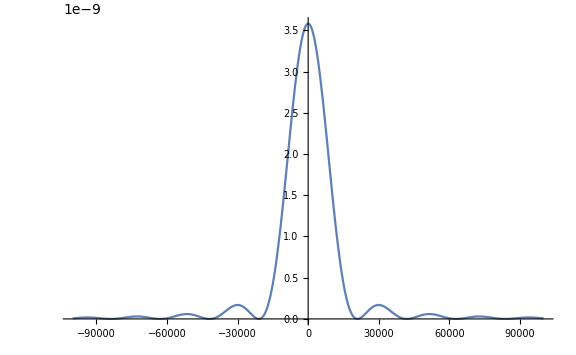

```mathematica
f=10^10;
p=0.3*10^-3;
pulse[t_]:=Sin[f t]*HeavisideTheta[t]*HeavisideTheta[p-t];
freq=FourierTransform[pulse[t],t,ω];
psd=Abs[freq]^2;Plot[psd/.ω->w-f,{w,-10^5,+10^5},PlotRange->All,ImageSize->Large]
```